# QNMs of a Horizonless Compact Object

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* !! continuare la costruzione a blocchi di "QNM_ECO1_heoc_8.m" (ultimo ϵ = 10^-6) !! *)
```

1) Sistemare sezione plot (rif. anche a “QNM_Schwarzschild.nb”)

## Non-rotating Case

## Computing the QNMs

Follows the implementation of part of the QNM calculation method. We emulate the method used in the non-rotating BH case.

This Section focuses on the search for approximate solutions near the ECO’s surface and at infinity. BCs near the surface are the membrane paradigm’s BC itself and its analytical solution.
Check “QNM_Compute.nb” for the actual integrator and finder.

### Set-up

```mathematica
f[r_]:=1-(2 M)/r;VRW=f[r]((l(l+1))/r^2-(6 M)/r^3);
rs[r_]:=Simplify[Integrate[1/f[r],r],r>0];
EQRW=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-VRW)ψ[r];
```

```mathematica
Print["Tortoise coordinate r_* = ", rs[r]];
Print["Regge-Wheeler equation:\n", EQRW, " = 0"];
```

Tortoise coordinate r_* = r+2 M Log[-2 M+r]

Regge-Wheeler equation:
 (-((-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r))+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r] = 0

### Inner Boundary Condition

Since the object has no horizon the inner boundary (obviously) is set by its radius r_CO.
The outer boundary condition of a Schwarzschild BH is valid also in this case.

Magari implementare espansione in serie con funzione integrata sotto.

Cercare QNMs al variare di eps (fino a 1, i.e. stella di neutroni) e eta (tra 0 a 1/16π) con griglia abbastanza fitta e vedere la dipendenza del QNM da eps e eta. Se ci sono discontinuità è perché trova altri QNM (e.g. overtone) → griglia più fitta.

```mathematica
(* Membrane paradigm's BC from Eq. 11 of https://arxiv.org/pdf/2006.14628*)
α=(-(ⅈ ω)/(16π η)-r^2/(2(r-3M))V);(* -> -ⅈω in the BH case *)
ψMP=ψ[r]/.DSolve[{ψ'[r]f[r]==α ψ[r]},ψ[r],r][[1]]
```

ⅇ^((-16 π η Log[r]-8 (-2+l+l^2) π η Log[-3 M+r]-ⅈ ω (r+2 M Log[-2 M+r]))/(16 π η)) C[1]

```mathematica
Simplify[D[ψMP,r]f[r]-α ψMP]
```

0

```mathematica
(* Horizon BC in the BH case *)
ψBH=ψ[r]/.DSolve[{ψ'[r]f[r]==-ⅈ ω ψ[r]},ψ[r],r][[1]]
```

ⅇ^(-ⅈ ω (r+2 M Log[-2 M+r])) C[1]

```mathematica
BHHor=Simplify[Series[ψBH,{r,2M,0}]]
MPHor=Simplify[Series[ψMP/.η->1/(16π),{r,2M,0}]]
Simplify[Normal[BHHor]/Normal[MPHor]](* proportionality constant *)
```

(-2 M+r)^(-2 ⅈ M ω) (ⅇ^(-2 ⅈ M ω) C[1]+O[r-2 M]^1)

(-2 M+r)^(-2 ⅈ M ω) (-1/2 ⅇ^(-2 ⅈ M ω) (-M)^(-1/2 l (1+l)) C[1]+O[r-2 M]^1)

-2 (-M)^(1/2 l (1+l))

```mathematica
k=ω/(16π η);
ϕSur[r_]:=Exp[-ⅈ k rs[r]] h[r]/(r(r-3M)^((l^2+l-2)/2));
```

### Expansion at the horizon

```mathematica
k=ω/(16π η);
ϕSur[r_]:=Exp[-ⅈ k rs[r]](r-3M)^((l(l+1))/2-1)/r g[r];
sSur=Simplify[Exp[ⅈ k r]×EQ/.{ψ[r]->ϕSur[r],ψ'[r]->ϕSur'[r],ψ''[r]->ϕSur''[r]}]
```

ⅇ^((ⅈ r ω)/(16 π η)) EQ

```mathematica
ϕSur[r_]:=(r-2M)^(-2M ⅈ k)(r-3M)^((l(l+1))/2-1)/r g[r];
CT=(r-2M)^(-2M ⅈ k)(r-3M)^((l(l+1))/2-3);
sSur=Simplify[EQ/.{ψ[r]->ϕSur[r],ψ'[r]->ϕSur'[r],ψ''[r]->ϕSur''[r]}];
GSur[r_]:=Sum[gSur[i](r-2 M)^i,{i,0,5}];
Simplify[Series[sSur/.{η->1/(16π),g[r]->GSur[r],g'[r]->GSur'[r],g''[r]->GSur''[r]},{r,2M,1}]]
```

(-2 M+r)^(-2 ⅈ M ω) (((-M)^(1/2 l (1+l)) ((-2+l+ⅈ M ω-2 ⅈ l M ω-4 M^2 ω^2+l^2 (1-2 ⅈ M ω)) gSur[0]+M (-1+4 ⅈ M ω) gSur[1]) (r-2 M))/(8 M^5)+O[r-2 M]^2)

```mathematica
Simplify[Series[sSur,{r,2M,0}]]
```

(-2 M+r)^(-(ⅈ M ω)/(8 π η)) (((-M)^(1/2 (-6+l+l^2)) M (-1+256 π^2 η^2) ω^2 g[2 M])/(512 π^2 η^2)+O[r-2 M]^1)

```mathematica
Simplify[Series[sHor,{r,2M,0}]]
```

(-((-3+l+l^2-2 ⅈ M ω-8 M^2 ω^2) g[2 M])+2 M (1-4 ⅈ M ω) g'[2 M])/(8 M^3)+O[r-2 M]^1

```mathematica
ϕHor[r_]:=(r-2M)^(-2 M ⅈ ω)g[r];(* the term e^-ⅈωr can be neglected since it doesn't go to 0 when r->0 *)
CT=(r-2M)^(1-2M ⅈ ω);
sHor=Simplify[EQ/CT/.{ψ[r]->ϕHor[r],ψ'[r]->ϕHor'[r],ψ''[r]->ϕHor''[r]}];
GHor[r_]:=Sum[gHor[i](r-2 M)^i,{i,0,5}];
Simplify[Series[sHor/.{g[r]->GHor[r],g'[r]->GHor'[r],g''[r]->GHor''[r]},{r,2M,1}]]
```

(-((-3+l+l^2-2 ⅈ M ω-8 M^2 ω^2) gHor[0])+2 M (1-4 ⅈ M ω) gHor[1])/(8 M^3)+((3 (-4+l+l^2-2 ⅈ M ω-4 M^2 ω^2) gHor[0]-2 M (l gHor[1]+l^2 gHor[1]-2 M (5 ⅈ ω gHor[1]+4 M ω^2 gHor[1]+4 gHor[2]-8 ⅈ M ω gHor[2]))) (r-2 M))/(16 M^4)+O[r-2 M]^2

```mathematica
(* Series coefficients *)
CoefSur[ord_]:=Module[{G,EQ,CT,s},
G[r_]:=Sum[gSur[i](r-2 M(1+ϵ))^i,{i,0,ord+5}];
EQ=sSur/.{g[r]->G[r],g'[r]->G'[r],g''[r]->G''[r]};
CT=(2^-9(2 M ϵ)^((-ⅈ M ω)/(8 π η)))/(M^4 π^2 η^2(1+ϵ)^4(2ϵ-1)^3);
s=Simplify[Series[EQ,{r,2M(1+ϵ),ord}]/CT];

Simplify[Solve[Table[SeriesCoefficient[s,i],{i,0,ord}]==0,Table[gSur[i],{i,2,ord+2}]]]
]
```

```mathematica
ordSur=2;coef=CoefSur[ordSur][[1]];
```

```mathematica
gi=Table[gSur[i],{i,2,ordSur+2}]/.coef;
coefs=CoefficientList[gi,{gSur[0],gSur[1]}];(* for each gSur[i>=1] the output is a 2D array. The indexing 'set' the degree of the variable *)
```

```mathematica
coef0=coefs[[;;,2,1]];
coef1=coefs[[;;,1,2]];
```

```mathematica
Series[coef0[[1]]/.{η->1/(16π),l->2},{ϵ,0,0}]
```

-(ⅈ (2 ⅈ+5 M ω))/(2 M^2 ϵ)-(2 ⅈ (-ⅈ+3 M ω))/M^2+O[ϵ]^1

```mathematica
coefHor=Import["CoefHor_Schw.m"];
coefHor[[;;3]]/.{hHor[0]->1}
```

{hHor[1]→(ⅈ (3-2 ⅈ M ω-8 M^2 ω^2))/(2 M (ⅈ+4 M ω)),hHor[2]→-(32-4 (3+8 M^2 ω^2)-4 (5+16 M^2 ω^2)+4 (3-3 ⅈ M ω+10 M^2 ω^2+12 ⅈ M^3 ω^3+16 M^4 ω^4))/(16 M^2 (ⅈ+2 M ω) (ⅈ+4 M ω)),hHor[3]→-1/(96 M^3 (ⅈ+2 M ω) (ⅈ+4 M ω) (3 ⅈ+4 M ω))ⅈ (160+16 (-8+6 ⅈ M ω-24 M^2 ω^2)-24 (7-4 ⅈ M ω+16 M^2 ω^2)+12 (9-12 ⅈ M ω+20 M^2 ω^2+8 ⅈ M^3 ω^3+32 M^4 ω^4)+4 (43-66 ⅈ M ω+96 M^2 ω^2+48 ⅈ M^3 ω^3+192 M^4 ω^4)-4 (27-63 ⅈ M ω+36 M^2 ω^2-48 ⅈ M^3 ω^3+56 M^4 ω^4+192 ⅈ M^5 ω^5+128 M^6 ω^6))}

```mathematica
x2=hHor[2]/.coefHor[[2]]/.{hHor[0]->1}
```

-(2 l^3+l^4-2 l (3+8 M^2 ω^2)-l^2 (5+16 M^2 ω^2)+4 (3-3 ⅈ M ω+10 M^2 ω^2+12 ⅈ M^3 ω^3+16 M^4 ω^4))/(16 M^2 (ⅈ+2 M ω) (ⅈ+4 M ω))

```mathematica
gSur[1]/.Solve[Simplify[x1-x2]==0,gSur[1]][[1]]
```

(8 ⅈ-4 ⅈ l-4 ⅈ l^2+20 ⅈ ϵ-14 ⅈ l ϵ-11 ⅈ l^2 ϵ+6 ⅈ l^3 ϵ+3 ⅈ l^4 ϵ+56 M ω-32 l M ω-32 l^2 M ω+108 M ϵ ω-72 l M ϵ ω-60 l^2 M ϵ ω+24 l^3 M ϵ ω+12 l^4 M ϵ ω-112 ⅈ M^2 ω^2+80 ⅈ l M^2 ω^2+80 ⅈ l^2 M^2 ω^2-312 ⅈ M^2 ϵ ω^2+192 ⅈ l M^2 ϵ ω^2+176 ⅈ l^2 M^2 ϵ ω^2-32 ⅈ l^3 M^2 ϵ ω^2-16 ⅈ l^4 M^2 ϵ ω^2-64 M^3 ω^3+64 l M^3 ω^3+64 l^2 M^3 ω^3-432 M^3 ϵ ω^3+192 l M^3 ϵ ω^3+192 l^2 M^3 ϵ ω^3+64 ⅈ M^4 ϵ ω^4)/(4 M (ⅈ+2 M ω) (ⅈ+4 M ω) (ⅈ+ⅈ ϵ-2 ⅈ l ϵ-2 ⅈ l^2 ϵ+4 M ω+4 M ϵ ω))

### QNM finder

The functions to integrate the Regge-Wheeler equation and to find QNMs are implemented in “QNM_Compute.nb” in a generalized form.
Here follow components specific for non-spinning ECOs, referring to the approximate solutions computed in the previous Sections. 

!! NOTE: when running a computation check out everything necessary has been defined. !!

```mathematica
SubsHE[in_]:={η->in[[1]],eps->in[[2]]};(* maybe this definition can be avoided... *)
```

```mathematica
(* --- EcoBC --- *)
(* coefI  : empty list (the horizon BC is completely defined inside - here for compatibility) *)
(* coefE  : list of substitution rules for the series coefficients at infinity *)
(* output : list of two boundary conditions (see QNM_Compute.nb for applications) *)
EcoBC[coefI_,coefE_]:=Module[{ordI,bcI,ordE,bcE},
k=ω/(16π η);
ordI=Length[coefI];bcI=Exp[-ⅈ k rs[r]](r-3M)^((l(l+1))/2-1)/r;
ordE=Length[coefE];bcE=Exp[ⅈ ω rs[r]]Sum[gInf[i] r^-i,{i,0,ordE}]//.coefE;

Return[{bcI,bcE}];
];
```

```mathematica
coefInf=Import["SeriesCoef\\CoefInf_Schw_10.m"];
```

### Past integrators (here for knowledge)

```mathematica
(* Integrator V2.5 - mathematically identical to V2 but with forced minimum precision *)
IntQNM[ω0_,ECO_,theta_,coefInf_]:=Module[{rules,param,prec,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};

param=Union[{M->1,ω->ω0,gInf[0]->1},Thread[{η,ϵ}->ECO],Thread[{l,match,inf}->theta]];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rHor=2M(1+ϵ)/.param;
rm=match×M/.param;
rInf=inf×M/.param;

EQs=SetPrecision[{EQ==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}],prec];

(* Integration from the horizon *)
ξHor=Exp[1/(16 π η)(-16 π η Log[r]-8 (-2+l+l^2) π η Log[-3 M+r]-ⅈ ω (r+2 M Log[-2 M+r]))]//.param;
BCs=SetPrecision[{ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor},prec];(* boundary conditions with at least 20 digits *)

ψHor=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules][[1]];

(* Integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs=SetPrecision[{ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf},prec];(* boundary conditions with at least 20 digits *)

ψInf=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules][[1]];

(* Linear combination *)
b=ψHor/ψInf/.r->rm;(* coefficient of the linear combination such that ψn is continuous at r=rm *)
(* ψn=Piecewise[{{ψHor,r<rm},{b×ψInf,r≥rm}}]; (* final function *) *)

Δψp=(D[ψHor,r]-D[b ψInf,r])/D[ψHor,r]/.r->rm;
{Δψp}
]
```

```mathematica
(* Integrator test *)
IntQNM[2/5-1/10 ⅈ,{1/(16π),10^-5},{2,10,50},coefInf][[1]]
```

2.010893861348067-0.0718837600682219 ⅈ

FINDER

The QNM is estimated searching the root of the integrator’s output.

```mathematica
FindQNM[ωguess_,ECO_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,ECO,{2,10,50},coefInf][[1]];(* watch out for differences in input parameters *)
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20(*,EvaluationMonitor:>Print["ω = ", x," Δψ' = ",Abs[g[x]]]*)][[1]];
Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
FindQNM[2/5-1/10 ⅈ,{1/(16π),10^-10}]
```

{0.37367169525216649296-0.088962293530515817318 ⅈ,4.×10^-16}

```mathematica
FindQNM[2/5-1/10 ⅈ,{1/(16π),10^-10}][[1]]-ωSBH
```

1.08341×10^-8+2.21584×10^-8 ⅈ

INTEGRATOR VERSION 1

We adopt a direct integration method.
The master equation is solved numerically from infinity, using BH’s boundary conditions (see QNM_Schwarzschild_FV.nb).
The output is the membrane paradigm’s BC (see above).

```mathematica
(* Integrator V1 *)
IntQNM[ω0_,value_,coefInf_]:=Module[{rules,param,rHor,rInf,ξ,ξInf,EQs,BCs,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->MachinePrecision};
param=Union[{M->1,ω->ω0,gInf[0]->1},Thread[{l,η,ϵ,inf}->value]];

rHor=2M(1+ϵ)/.param;
rInf=inf×M/.param;

EQs={EQ==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}];

(* Integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs={ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf};
sol=NDSolve[Union[EQs,BCs],ξ,{r,rInf,rHor},rules];
ψn=ξ[r]/.sol[[1]];

(* Membrane paradigm's BC *)
Δψp=D[ψn,r]f[r]-α ψn/.Union[{r->rHor},param];
{Δψp}
]
```

INTEGRATOR VERSION 2

We emulate the method used in the non-rotating BH case (see QNM_Schwarzschild_FV.nb).
The BCs at the horizon are the membrane paradigm’s BC itself and its analytical solution.
The output is the derivative deviation at the match point.

```mathematica
(* Integrator V2 *)
IntQNM[ω0_,ECO_,value_,coefInf_]:=Module[{rules,param,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};
param=Union[{M->1,ω:>SetPrecision[ω0,Max[Precision[ω0],20]],gInf[0]->1},Thread[{η,ϵ}->ECO],Thread[{l,match,inf}->value]];

rHor=2M(1+ϵ)/.param;
rm=match×M/.param;
rInf=inf×M/.param;

EQs={EQ==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}];

(* Integration from the horizon *)
ξHor=Exp[(-16 π η Log[r]-8 (-2+l+l^2) π η Log[-3 M+r]-ⅈ ω (r+2 M Log[-2 M+r]))/(16 π η)]//.param;
BCs={ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor};
solHor=NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules];
ψHor=ξ[r]/.solHor[[1]];

(* Integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs={ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf};
solInf=NDSolve[Union[EQs,BCs],ξ,{r,rInf,rHor},rules];
ψInf=ξ[r]/.solInf[[1]];

(*Linear combination*)
b=ψHor/ψInf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
ψn=Piecewise[{{ψHor,r<rm},{b×ψInf,r≥rm}}];
Δψp=(D[ψHor,r]-D[b ψInf,r])/D[ψHor,r]/.r->rm;
{Δψp}
]
```

## Parameter space study

```mathematica
ωSBH=(0.7473433688360838`20- 0.1779246313778714`20ⅈ)/2;(* analytical value of Schwarzschild BH's n=1 QNM *)
Print["For a Schwarzschild BH: ω_0 = ", ωSBH]
```

For a Schwarzschild BH: ω_0 = 0.3736716844180419-0.0889623156889357 ⅈ

### Membrane Paradigm Parameters (η, ϵ)

```mathematica
x={};step={{1/8,2-1/8,1/8},{2+1/4,10,1/4},{2,2+1/5,1/20}};
Do[x=Union[x,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
x=ReverseSort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
```

```mathematica
y={};step={{6+1/8,10,1/8}};
Do[y=Union[y,Table[j,{j,i[[1]],i[[2]],i[[3]]}]],{i,step}];
y=ReverseSort[y];ϵarray=10^-y;
```

```mathematica
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Print["N = ",Length[ηarray]," η_in = ",ηarray[[1]]//N," η_fin = ",ηarray[[-1]]//N ];
Print["N = ",Length[ϵarray]," ϵ_in = ",ϵarray[[1]]//N," ϵ_fin = ",ϵarray[[-1]] //N];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944

N = 32 ϵ_in = 1.×10^-10 ϵ_fin = 7.49894×10^-7

```mathematica
P1=ListPlot[Transpose[{x,ηarray}],PlotRange->All];
P2=ListPlot[Transpose[{y,ϵarray}],PlotRange->All,ScalingFunctions->"Log10"];
GraphicsGrid[{{P1,P2}},ImageSize->Large]
```

### Computation

```mathematica
(* Dim[η] × Dim[ϵ] output with elements (η, ϵ, ω, check). Saving in a new file, for farther options see "QNM_compute.nb" *)

(* Default: running over η then ϵ *)
new=Table[{},{i,ηarray},{j,ϵarray}];switch=False;
If[switch,new=new//Transpose;ECO=ECO//Transpose(* running over ϵ then η *)];

Monitor[Do[Do[new[[j,i]]=Join[ECO[[j,i]],FindQNM[ωguess,ECO[[j,i]]]];
ωguess=new[[j,i,3]],{j,1,Dimensions[ECO][[1]]}];
ωguess=new[[1,i,3]],{i,1,Dimensions[ECO][[2]]}],Row[{"ij = ",{i,j}}]];

new//Dimensions
```

```mathematica
If[switch,new=new//Transpose];out=new;
Print["Dim[out] = ",out//Dimensions];
```

```mathematica
Export["QNM_ECO1_heoc_8.m",out];Clear[out];(* ECO1 i.e. non-rotating ECO *)
```

### Data Analysis

NOTE: in generale è molto sensibile alla combinazione tra guess e parametri. Quindi se si parte dal risultato di un set di parametri bisogna allontanarsi ‘poco’ perché converga. Bisogna partire da un QNM noto e muoversi lentamente (potenzialmente variando un parametro alla volta).

```mathematica
(* Old file set-up. The grid must be generated again *)
in=Import["QNM_ECO1_he_7.dat"]//ToExpression;
Roh=Table[{ηarray[[i]],Re[in[[i,j]]]},{j,1,Length[ϵarray]},{i,1,Length[ηarray]}];
Ioh=Table[{ηarray[[i]],-Im[in[[i,j]]]},{j,1,Length[ϵarray]},{i,1,Length[ηarray]}];
Roe=Table[{ϵarray[[j]],Re[in[[i,j]]]},{i,1,Length[ηarray]},{j,1,Length[ϵarray]}];
Ioe=Table[{ϵarray[[j]],-Im[in[[i,j]]]},{i,1,Length[ηarray]},{j,1,Length[ϵarray]}];
```

```mathematica
(* Current file set-up: matrix with elements (η, ϵ, ω, check) *)
in1=Import["Data_GSearch\\ECO1_10_50_10_heRIc_-1_1.m"];
Print["Dim[in1] = ", in1//Dimensions];
```

Dim[in1] = {161,5}

```mathematica
(* Real and imaginary part as function of η - remeber Extract *)
Roh1=in1[[;;,;;,1;;3;;2]]//Transpose;Roh1[[;;,;;,2]]=Re[Roh1[[;;,;;,2]]];
Ioh1=in1[[;;,;;,1;;3;;2]]//Transpose;Ioh1[[;;,;;,2]]=-Im[Ioh1[[;;,;;,2]]];
ch1=in1[[;;,;;,1;;4;;3]]//Transpose;

(* Real and imaginary part as function of ϵ *)
Roe1=in1[[;;,;;,2;;3]];Roe1[[;;,;;,2]]=Re[Roe1[[;;,;;,2]]];
Ioe1=in1[[;;,;;,2;;3]];Ioe1[[;;,;;,2]]=-Im[Ioe1[[;;,;;,2]]];
ce1=in1[[;;,;;,2;;4;;2]];
```

```mathematica
in2=Import["QNM_ECO1_heoc_52.m"];Print["Dim[in2] =",in2//Dimensions];

(* Real and imaginary part as function of η - remeber Extract *)
Roh2=in2[[;;,;;,1;;3;;2]]//Transpose;Roh2[[;;,;;,2]]=Re[Roh2[[;;,;;,2]]];
Ioh2=in2[[;;,;;,1;;3;;2]]//Transpose;Ioh2[[;;,;;,2]]=-Im[Ioh2[[;;,;;,2]]];
ch2=in2[[;;,;;,1;;4;;3]]//Transpose;

(* Real and imaginary part as function of ϵ *)
Roe2=in2[[;;,;;,2;;3]];Roe2[[;;,;;,2]]=Re[Roe2[[;;,;;,2]]];
Ioe2=in2[[;;,;;,2;;3]];Ioe2[[;;,;;,2]]=-Im[Ioe2[[;;,;;,2]]];
ce2=in2[[;;,;;,2;;4;;2]];
```

#### File: “ECO1_10_50_10_heRIc_-1_1.m”

```mathematica
(* NOTE: modify output to return a 3D matrix for compatibility *)
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," ϵ_in = ",in1[[1,2]]//N," ϵ_fin = ",in1[[-1,2]]//N];
```

N = 161 ϵ_in = 1.×10^-8 ϵ_fin = 1.

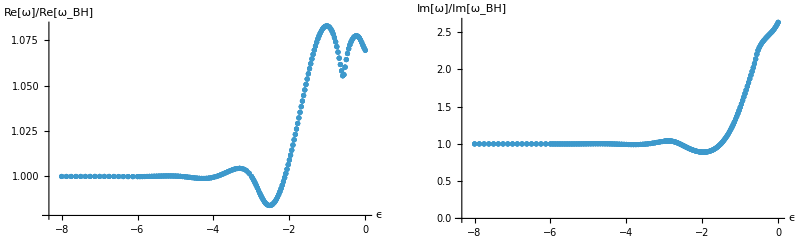

```mathematica
Roe1=in1[[;;,2;;3;;1]];Roe1[[;;,2]]/=Re[ωSBH];
Ioe1=in1[[;;,2;;4;;2]];Ioe1[[;;,2]]/=Im[ωSBH];
PR=ListPlot[Roe1,AxesLabel->{"ϵ","Re[ω]/Re[ω_BH]"},ScalingFunctions->{"Log10",None}(*,Joined->True*),Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1,AxesLabel->{"ϵ","Im[ω]/Im[ω_BH]"},ScalingFunctions->{"Log10",None}(*,Joined->True*),Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Full]
```

#### File: “QNM_ECO1_heoc_6.m”

Starting from η ∼ 0. Already at ϵ=10^(9+1/2) it gives the same result for the first values of η. For η ∼ [0.01954, 0.01989] the result seems to acquire physical meaning, but higher η still give strange results.

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 44 η_in = 0.0049757 η_fin = 0.0198944

N = 21 ϵ_in = 1.×10^-10 ϵ_fin = 1.

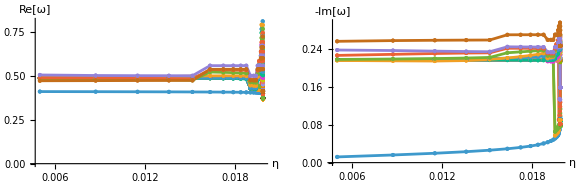

```mathematica
PR=ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

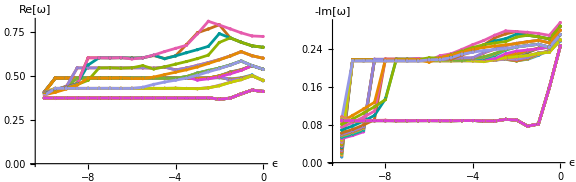

```mathematica
PR=ListPlot[Roe1[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

```mathematica
(* plots of interesting parts *)
```

#### File: “QNM_ECO1_heoc_8.m”

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944

N = 101 ϵ_in = 1.×10^-10 ϵ_fin = 1.

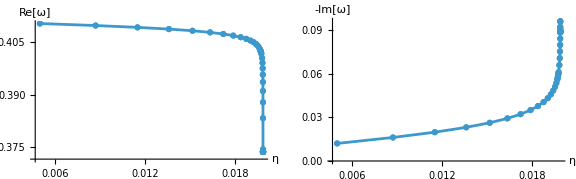

```mathematica
PR=ListPlot[Roh1[[;;1]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;1]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

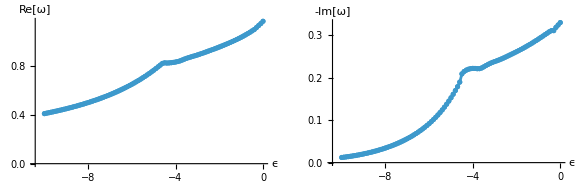

```mathematica
PR=ListPlot[Roe1[[;;1]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[;;1]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

```mathematica
(* plots of interesting parts *)
```

#### File: “QNM_ECO1_heoc_34.m”

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 52 η_in = 0.0198944 η_fin = 0.0049757

N = 49 ϵ_in = 1.×10^-10 ϵ_fin = 0.0001

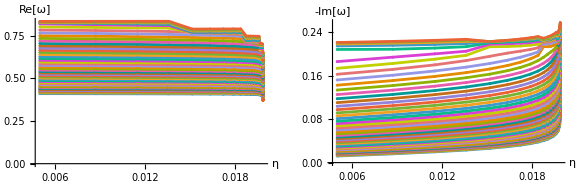

```mathematica
PR=ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

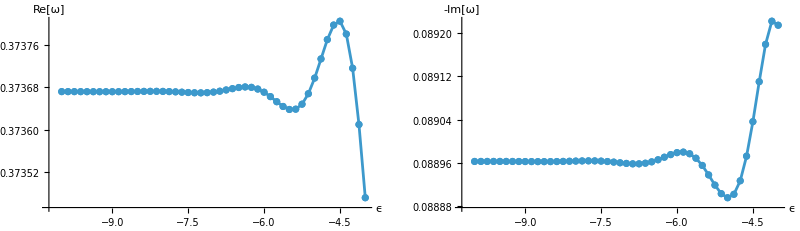

```mathematica
PR=ListPlot[Roe1[[1]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[1]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Full]
```

#### File: “QNM_ECO1_heoc_35.m”

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 16 η_in = 0.0049757 η_fin = 0.0196954

N = 61 ϵ_in = 1.×10^-10 ϵ_fin = 0.0001

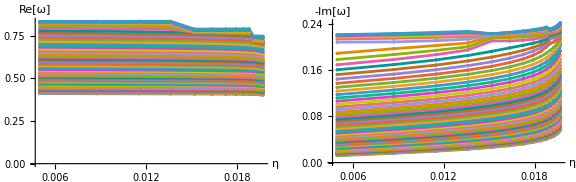

```mathematica
PR=ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

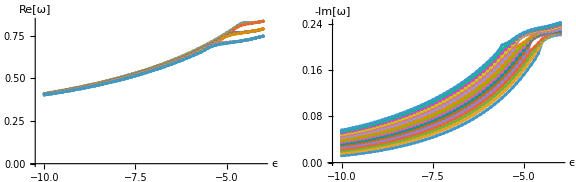

```mathematica
PR=ListPlot[Roe1[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

#### File: “QNM_ECO1_heoc_52.m”

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 52 η_in = 0.0198944 η_fin = 0.0049757

N = 32 ϵ_in = 1.×10^-10 ϵ_fin = 7.49894×10^-7

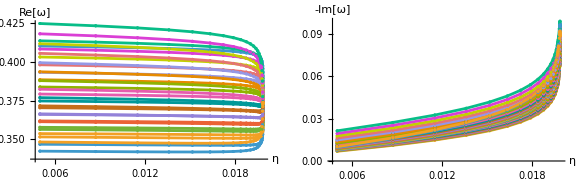

```mathematica
PR=ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

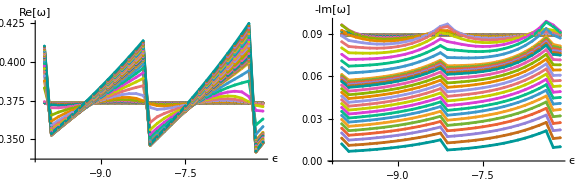

```mathematica
PR=ListPlot[Roe1[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

#### File: “QNM_ECO1_heoc_53.m”

```mathematica
(* grid range *)
Print["N = ",Dimensions[in1][[1]]," η_in = ",in1[[1,1,1]]//N," η_fin = ",in1[[-1,1,1]]//N];
Print["N = ",Dimensions[in1][[2]]," ϵ_in = ",in1[[1,1,2]]//N," ϵ_fin = ",in1[[1,-1,2]]//N];
```

N = 52 η_in = 0.0049757 η_fin = 0.0198944

N = 32 ϵ_in = 1.×10^-10 ϵ_fin = 7.49894×10^-7

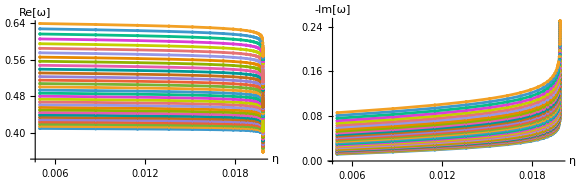

```mathematica
PR=ListPlot[Roh1[[;;]],AxesLabel->{"η","Re[ω]"},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioh1[[;;]],AxesLabel->{"η","-Im[ω]"},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

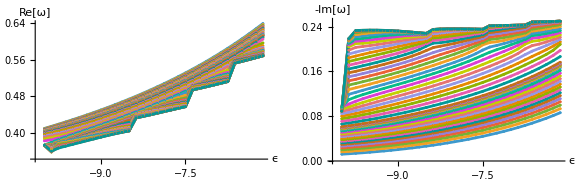

```mathematica
PR=ListPlot[Roe1[[;;]],AxesLabel->{"ϵ","Re[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
PI=ListPlot[Ioe1[[;;]],AxesLabel->{"ϵ","-Im[ω]"},ScalingFunctions->{"Log10",None},Joined->True,Mesh->Full,PlotRange->All];
GraphicsGrid[{{PR,PI}},ImageSize->Large]
```

```mathematica
(* plots of interesting parts *)
```

### Past plots

Results from integrator V2:
	“QNM_ECO1_he_1.dat”.
Results from integrator V2.5:
	“QNM_ECO1_he_2.dat” - error messages persist during the evaluation,
	“QNM_ECO1_he_3.dat”,
	“QNM_ECO1_he_4.dat”,
	“QNM_ECO1_he_5.dat” - division by zero appeared during evaluation.

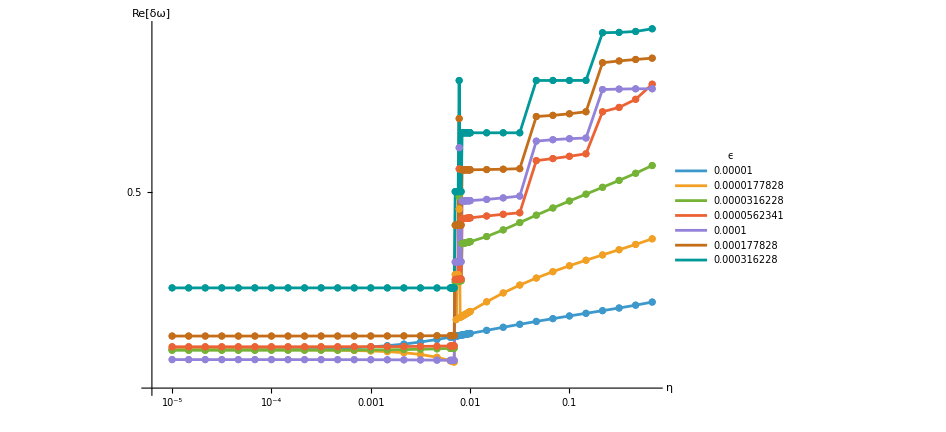

```mathematica
ListPlot[Rωηp[[;;;;3]],PlotLegends->LineLegend[Automatic,ϵarray//N,LegendLabel->"ϵ"],ImageSize->700,AxesLabel->{"η","Re[δω]"},ScalingFunctions->{"Log","Log"},Joined->True,Mesh->Full,PlotRange->All](*{{0.0196,0.0198},{0.3,0.8}}*)
```

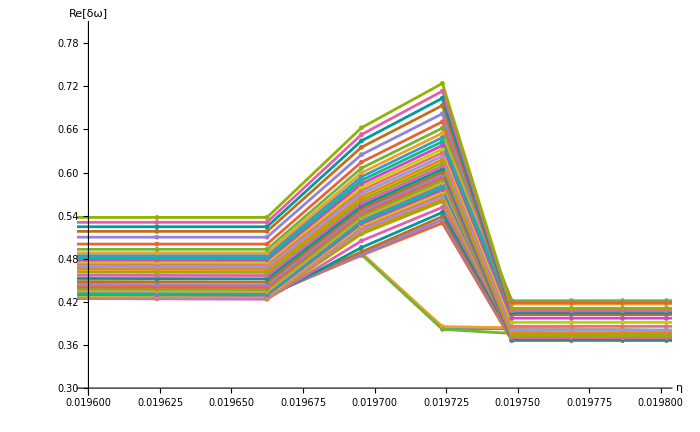

```mathematica
ListPlot[Re[ωη[[All]]](*,PlotLegends->LineLegend[Automatic,ϵarray//N,LegendLabel->"ϵ"]*),ImageSize->700,AxesLabel->{"η","Re[δω]"},ScalingFunctions->{None,None},Joined->True,Mesh->Full,PlotRange->{{0.0196, 0.0198}, {0.3, 0.8}}]
```

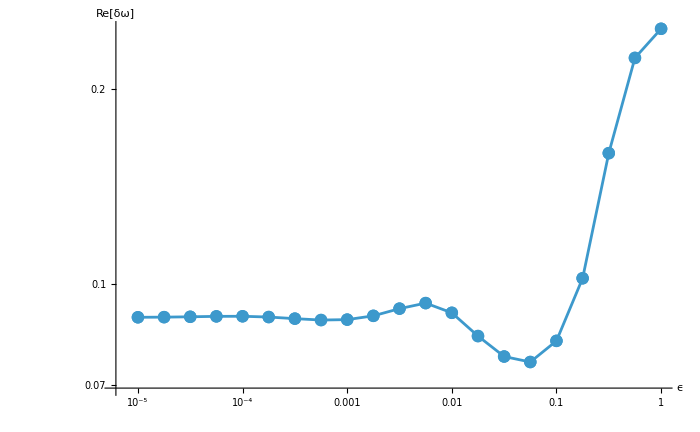

```mathematica
ListPlot[Iωϵ[[1]],PlotLegends->LineLegend[Automatic,ηarray[[All]]//N,LegendLabel->"η"],ImageSize->700,AxesLabel->{"ϵ","Re[δω]"},ScalingFunctions->{"Log","Log"},Joined->True,Mesh->Full,PlotRange->All](*{{10^-5,10^-3},{0.38,0.37}}*)
```

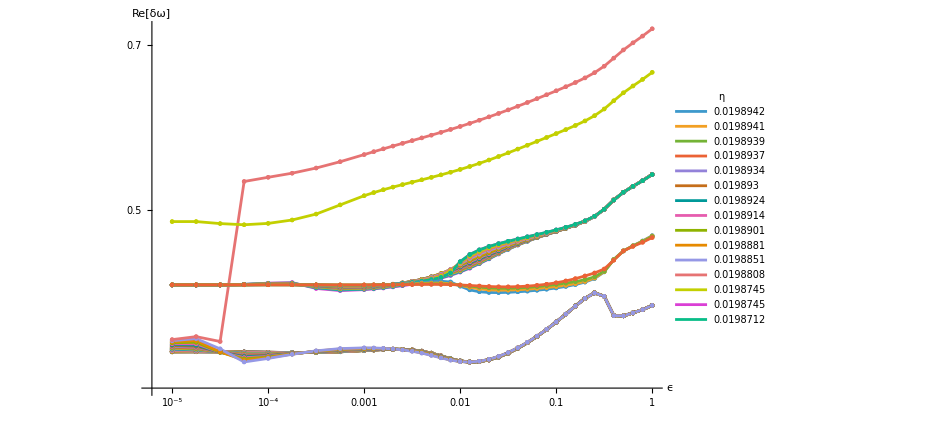

```mathematica
ΔωR=Abs[(Re[ωimport]-Re[ωSBH])/Re[ωSBH]];ΔωI=Abs[(Im[ωimport]-Im[ωSBH])/Im[ωSBH]];
```

```mathematica
ΔRη=Table[{ηarray[[i]],ΔωR[[i,j]]},{j,1,Dimensions[ΔωR][[2]]},{i,1,Dimensions[ΔωR][[1]]}];
ΔIη=Table[{ηarray[[i]],ΔωI[[i,j]]},{j,1,Dimensions[ΔωI][[2]]},{i,1,Dimensions[ΔωI][[1]]}];
ΔRϵ=Table[{ϵarray[[j]],ΔωR[[i,j]]},{i,1,Dimensions[ΔωR][[1]]},{j,1,Dimensions[ΔωR][[2]]}];
ΔIϵ=Table[{ϵarray[[j]],ΔωI[[i,j]]},{i,1,Dimensions[ΔωI][[1]]},{j,1,Dimensions[ΔωI][[2]]}];
```

### Old grids and other stuff

Grid of “QNM_ECO1_he_6.dat”

```mathematica
step=1/6;x=Join[Table[i,{i,5,3,-step}],Table[i,{i,1-step,1,-step}]];
step=1/15;x=Join[x,Table[i,{i,3-step,1,-step}]];
ReverseSort[x];ηarray=(1-10^-x)/(16π);
step=1/4;y=Table[i,{i,5,3,-step}];
step=1/10;y=Join[y,Table[i,{i,3-step,0,-step}]];
ReverseSort[y];ϵarray=10^-y;
```

```mathematica
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];Dimensions[ECO]//Print;
```

Grid of “QNM_ECO1_he_7.dat”

```mathematica
step1=1/6;step2=1/30;
x=Join[Table[i,{i,5,2+4/20,-step1}],Table[i,{i,2+4/20,2,-step2}],Table[i,{i,2,step1,-step1}]];ηarray=(1-10^-x)/(16π);
y=Table[i,{i,5+1/2,0,-1/2}];ϵarray=10^-y;
parECO=Table[{h,e},{h,ηarray},{e,ϵarray}];Dimensions[parECO]
```

{36,12,2}

Grid of “QNM_ECO1_heoc_1.m”. Note that the data structure is a matrix with elements (η, ϵ, ω, check)

```mathematica
step1=1/6;step2=1/100;
x=Join[Table[i,{i,5,2+4/20,-step1}],Table[i,{i,2+4/20,2,-step2}],Table[i,{i,2,step1,-step1}]];ηarray=(1-10^-x)/(16π);
y=Table[i,{i,5,0,-1/4}];ϵarray=10^-y;
```

{50,21,2}

Grid of “QNM_ECO1_heoc_2.m”. Note that the data structure is a matrix with elements (η, ϵ, ω, check).
QNMs vs η with fixed ϵ=10^-10.

```mathematica
step=1/8;x=Join[Table[i,{i,10,2+1/5+step,-step}],Table[i,{i,2-step,step,-step}]];
step=1/20;x=Join[x,Table[i,{i,2+1/5,2,-step}]];
x=ReverseSort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
y={10};ϵarray=10^-y;
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Dimensions[ECO]
```

{82,1,2}

Grid of  “QNM_ECO1_heoc_4.m”. Starting from η ∼ 0 and ϵ=10^-10.

```mathematica
step=1/8;x=Join[Table[i,{i,10,2+1/5+step,-step}],Table[i,{i,2-step,step/4,-step}]];
step=1/20;x=Join[x,Table[i,{i,2+1/5,2,-step}]];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
y={10};ϵarray=10^-y;
ECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Dimensions[ECO]
```

{82,1,2}

Grid of  “QNM_ECO1_heoc_5.m”. Starting from η ∼ 0 and varying ϵ.

```mathematica
step=1/3;x=Table[i,{i,10,2+step,-step}];
step=1/8;x=Union[x,Table[i,{i,2-step,step,-step}]];
step=1/20;x=Union[x,Table[i,{i,2+1/5,2,-step}]];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
step=1/2;y=Table[i,{i,10,3,-step}];
step=1/2;y=Union[y,Table[i,{i,3-step,0,-step}]];
y=ReverseSort[y];
ϵarray=10^-y;
```

Grid of  “QNM_ECO1_heoc_7.m”. Starting from η ∼ 0 and varying ϵ.

```mathematica
step=1/3;x=Table[i,{i,10,2+step,-step}];
step=1/8;x=Union[x,Table[i,{i,2-step,step,-step}]];
step=1/20;x=Union[x,Table[i,{i,2+1/5,2,-step}]];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
step=1/10;y=Table[i,{i,6-step,3,-step}];
(*step=1/5;y=Union[y,Table[i,{i,6-step,3,-step}]];*)
y=ReverseSort[y];
ϵarray=10^-y;
```

Grid of  “QNM_ECO1_heoc_8.m”. Working in blocks.

```mathematica
step=1/4;x=Table[i,{i,10,2+step,-step}];
step=1/8;x=Union[x,Table[i,{i,2-step,step,-step}]];
step=1/20;x=Union[x,Table[i,{i,2+1/5,2,-step}]];
x=Sort[x];ηarray=(1-10^-x)/(16π);(* x = -Subscript[log, 10][η'] *)
step=1/10;y=Table[i,{i,2-step,0,-step}];
(*step=1/5;y=Union[y,Table[i,{i,6-step,3,-step}]];*)
y=ReverseSort[y];
ϵarray=10^-y;
```

Grid of “QNM_ECO1_he_5.dat”

```mathematica
step=1/10;x=Table[i,{i,5,0,-step}];
ReverseSort[x];ηarray=(1-10^-x)/(16π);
step=1/4;y=Table[i,{i,5,3,-step}];
step=1/10;y=Join[y,Table[i,{i,3-step,0,-step}]];
ReverseSort[y];ϵarray=10^-y;
```

Grid of “QNM_ECO1_he_4.dat”

```mathematica
(* V2 *)
ηarray=Table[1/(16π)Log[i+2]/Log[102],{i,10^2,0,-2}];
ϵarray=Table[10^(-5 Log[i+1]/Log[21]),{i,20,0,-1}];(* the upper limit is a NS *)
parECO=Table[{h,e},{h,ηarray},{e,ϵarray}];Dimensions[parECO]
```

{51,21,2}

Grid of “QNM_ECO1_he_3.dat”

```mathematica
(* O.G. ECO parameters grid *)
ηarray=Table[1/(8 π^2)ArcTan[i+1],{i,10^2,0,-5}];PrependTo[ηarray,1/(16π)];(* denser near BH limit (added manually) *)
ϵarray=Table[10^-i,{i,5,0,-1/4}];(* the upper limit is a NS *)
parECO=Table[{h,e},{h,ηarray},{e,ϵarray}];
Dimensions[parECO]
```

{22,21,2}

```mathematica
(* QNMs A - Dim[η] × Dim[ϵ] output with elements (ω, check) plus one row (0, ϵ) and one column (0, η) *)
ωguess=2/5-1/10 ⅈ;ωfound=Table[{},{i,1,Dimensions[ECO][[1]]}];
Monitor[Do[Do[AppendTo[ωfound[[i]],FindQNM[ωguess,ECO[[i,j]]]];
ωguess=ωfound[[i,-1,1]],{j,1,Dimensions[ECO][[2]]}];
ωguess=ωfound[[i,1,1]],{i,1,Dimensions[ECO][[1]]}],
Row[{"ij = ",{i,j}}]];
Dimensions[ωfound]
```

{6,6,2}

```mathematica
m=Table[i+j,{i,1,3},{j,1,3}];v=Table[i,{i,0,2}];
Transpose[Join[{v},Transpose[m]]]//MatrixForm
```

(0 | 2 | 3 | 4
1 | 3 | 4 | 5
2 | 4 | 5 | 6)

```mathematica
Join[{v},m]//MatrixForm
```

(0 | 1 | 2
2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
ωexport=Transpose[Join[{ηarray},Transpose[ωfound]]];
ωexport=Join[{Join[{0},ϵarray]},ωexport];Dimensions[ωexport]
```

{7,7}

```mathematica
Export["QNM_ECO1_he_7.dat",ωexport];(* ECO1 i.e. non-rotating ECO *)
```

```mathematica
(* Fetching data A *)
ωimport=ωexport;(*Import[""]//ToExpression;*)Dimensions[ωimport]//Print;
ηarray=ωimport[[2;;,1]];ϵarray=ωimport[[1,2;;]];
```

## Hyperparameters (match, inf)

```mathematica
(* See "QNM_compute.nb" for the computation *)
data=Import["QNM_ECO1_miod_3.m"];label={"μ","ι","ω","|Δω|"};
accept=Select[data,#[[-1]]<10^-7&];reject=Select[data,#[[-1]]>10^-3&];

Print["Dim[data] = ",data//Dimensions,"\tDim[accept] = ",accept//Dimensions,"\tDim[reject] = ",reject//Dimensions];
Print["μ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t ι_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]}];
```

Dim[data] = {1000,4}	Dim[accept] = {307,4}	Dim[reject] = {130,4}

μ_(min/max) = {5.00144,14.9943}	 ι_(min/max) = {30.0271,149.963}

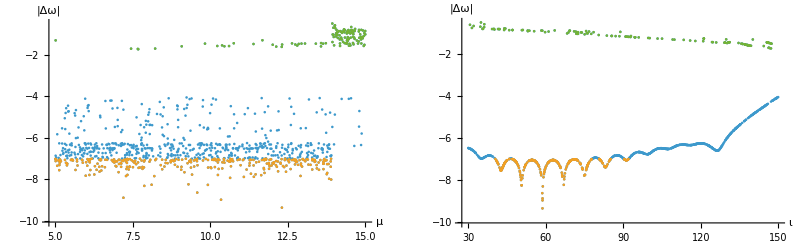

```mathematica
plots={};
Module[{index,l,point},
Do[index={i,-1};l=Extract[label,{{i},{-1}}];
point={Extract[data,{;;,index}],Extract[accept,{;;,index}],Extract[reject,{;;,index}]};
AppendTo[plots,ListPlot[point,AxesLabel->l,ScalingFunctions->{None,"Log10"},PlotRange->All]],
{i,2}]];

GraphicsGrid[{plots},ImageSize->Full]
```

```mathematica
Module[{a,b,c,l,point},
{a,b,c}={1,2,-1};l=Extract[label,{{a},{b},{c}}];
point={Extract[data,{;;,{a,b,c}}],Extract[accept,{;;,{a,b,c}}],Extract[reject,{;;,{a,b,c}}]};
P3D=ListPointPlot3D[point,AxesLabel->l,ScalingFunctions->{None,None,"Log10"}]];

𝕔={0.5,0.5,0.5};𝕣=3;
Animate[Show[P3D,ViewVector->{Scaled[𝕔+𝕣{Cos[f]Sin[t],Sin[f]Sin[t],Cos[t]}],Scaled[𝕔]}],{f,0,π/2},{t,π/2,0},AnimationRunning->False]
```

## Rotating Case

```mathematica
ωin=Import["QNM_ECO1_heoc_8.m"];
ωin//Dimensions
```

{52,61,4}

```mathematica
(* same ηs and adding ϵs *)
ωguess=ωin[[1,-1,3]];(* first η and last ϵ *)
ωnew=Table[{},{i,ϵarray},{j,ηarray}];

Monitor[Do[Do[ωnew[[j,i]]=Join[ECO[[i,j]],FindQNM[ωguess,ECO[[i,j]]]];
ωguess=ωnew[[j,i,3]],{i,1,Dimensions[ECO][[1]]}];
ωguess=ωnew[[j,1,3]],{j,1,Dimensions[ECO][[2]]}],Row[{"ij = ",{i,j}}]];

ωout=Join[ωin//Transpose,ωnew]//Transpose;
```

```mathematica
(* same ϵs *)
ωguess=ωout[[-1,1,3]];

Monitor[Do[Do[ωnew[[i,j]]=Join[ECO[[i,j]],FindQNM[ωguess,ECO[[i,j]]]];
ωguess=ωnew[[i,j,3]],{i,1,Dimensions[ECO][[1]]}];
ωguess=ωnew[[1,j,3]],{j,1,Dimensions[ECO][[2]]}],Row[{"ij = ",{i,j}}]];

ωout=Join[ωout,ωnew];
```